# Non-Linear Dynamics

## Logistic Map

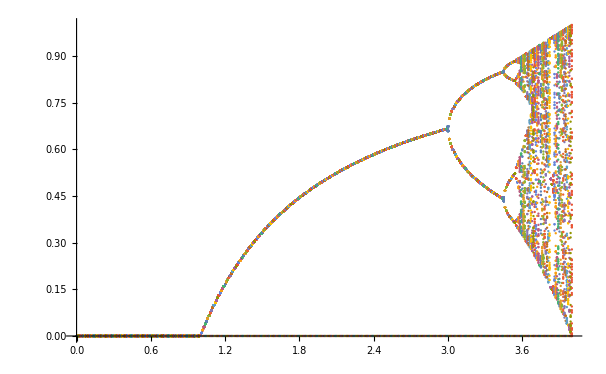

```mathematica
ListPlot[Table[Thread[{r,Nest[r # (1-#)&,Range[0,1,0.01],1000]}],{r,0,4,0.01}]]
```

## Julia Sets

```mathematica
JuliaSetPlot[z^2+I,z,ColorFunction->GrayLevel, PlotStyle->Opacity[.2, Red],PlotLegends->Automatic]
```

-Graphics-

## Mandelbrot Set

```mathematica
MandelbrotSetPlot[{-0.65+0.47 I,-0.4+.7I},PlotLegends->Automatic]
```

-Graphics-